```mathematica
ClearAll["Global`*"];
```

## Load the Bogoliubov coefficients

#### “BogCoefficientsAllMassesSmall.wl” works for 0 ≤ M_(ss,0),M_(bb,0) ≤ 9/4, switch to “BogCoefficientsAllMasses.wl” for constant masses >9/4

```mathematica
SetDirectory[NotebookDirectory[]];
<<"BogCoefficientsAllMassesSmall.wl";
(* <<"BogCoefficientsAllMasses.wl"; *)
```

These files contain: 
regIIIcoeffsSimp -- the Bogoliubov coefficients of the sharp feature’s excited state
αsols -- the WKB exponents during the feature are ±√α_i

#### Store the simplified coefficients in variables, match β phase convention

```mathematica
phaseConvention =-Exp[-2I κ(1-Exp[-δ/2])];
azz =αzz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
azs =αzs/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
azb =αzb/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
asz =αsz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
ass =αss/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
asb =αsb/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
abz =αbz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
abs =αbs/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
abb =αbb/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bzz = phaseConvention βzz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bzs =phaseConvention βzs /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bzb =phaseConvention βzb /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bsz =phaseConvention βsz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bss =phaseConvention βss /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bsb =phaseConvention βsb /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bbz =phaseConvention βbz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bbs =phaseConvention βbs /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bbb =phaseConvention βbb /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
```

WARNING!! :  these expressions are quite large and unwieldy, simplification and symbolic manipulation are very slow.
Plotting works fine though

```mathematica
LeafCount/@{azz,azs,azb,asz,ass,asb,abz,abs,abb}
```

{1247,19869,9276,1277,20258,9393,1299,20379,9286}

## Plots

### Plot the coefficient magnitudes (essentially same as Fig. 3.1)

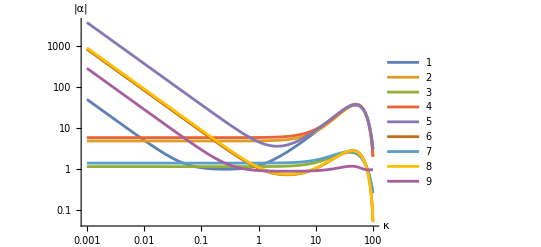

```mathematica
ClearAll[kk,ρ,Ω2f,mbb0,mss0,ξss,ξbb,Ω0,τ0,δ];
ρ=10.0;
Ω2f = 50;
plotvals={Ω0-> Ω2f Sin@ArcTan@ρ,τ0-> Ω2f Cos@ArcTan@ρ,mbb0-> 2.0,mss0-> 2.0,ξss-> -3,ξbb-> 0.0,δ-> 0.1};
αvals = αsols/.plotvals/.k-> κ k0/.k0-> 1;
LogLogPlot[Evaluate[ Abs/@{azz,azs,azb,asz,ass,asb,abz,abs,abb}/.plotvals/.αvals/.κ-> kk],{kk,10^-3,10^2},PlotLegends->Automatic,AxesLabel->{"κ","|α|"}]
```

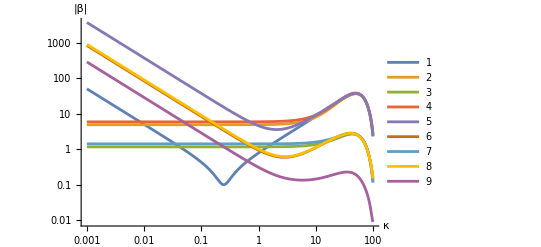

```mathematica
LogLogPlot[Evaluate[ Abs/@{bzz,bzs,bzb,bsz,bss,bsb,bbz,bbs,bbb}/.plotvals/.αvals/.κ-> kk],{kk,10^-3,10^2},PlotLegends->Automatic,AxesLabel->{"κ","|β|"}]
```

### Plot the enhancement of the adiabatic powerspectrum

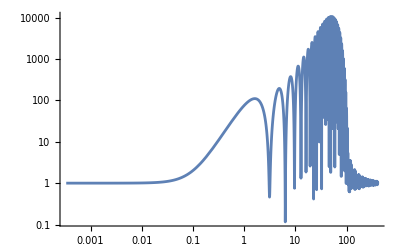

```mathematica
LogLogPlot[Evaluate[Abs[azz+ bzz]^2+Abs[azs+ bzs]^2+Abs[azb+bzb]^2/.plotvals/.αvals/.κ-> kk],{kk,Exp[-8],Exp[6]}]
```

### plot the WKB exponents

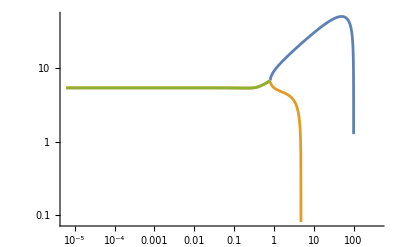

```mathematica
LogLogPlot[Evaluate[Abs/@Im/@Sqrt/@{α1,α2,α3}/.αsols/.plotvals/.k0-> 1/.k-> kk],{kk,Exp[-12],Exp[6]},PlotRange->Full]
```

## Spot check the quantization conditions (2.14)

```mathematica
kkk=10.0;
as={{azz,azs,azb},{asz,ass,asb},{abz,abs,abb}}/.plotvals/.αvals/.κ-> kkk;
bs={{bzz,bzs,bzb},{bsz,bss,bsb},{bbz,bbs,bbb}}/.plotvals/.αvals/.κ-> kkk;
```

```mathematica
id1=Table[Sum[as[[i,k]]Conjugate[as[[j,k]]]-Conjugate[bs[[i,k]]]bs[[j,k]],{k,3}],{i,3},{j,3}];
id2=Table[Sum[as[[i,k]] Conjugate[bs[[j,k]]]-Conjugate[bs[[i,k]]]as[[j,k]],{k,3}],{i,3},{j,3}];
```

```mathematica
id1//MatrixForm (* should be identity matrix*)
```

(1.+0. ⅈ | -4.62547×10^-13-4.26326×10^-14 ⅈ | 1.35447×10^-14-2.42861×10^-14 ⅈ
-4.62547×10^-13+4.26326×10^-14 ⅈ | 1.+0. ⅈ | 1.14006×10^-13-5.08482×10^-14 ⅈ
1.35447×10^-14+2.42861×10^-14 ⅈ | 1.14006×10^-13+5.08482×10^-14 ⅈ | 1.+0. ⅈ)

```mathematica
id2//MatrixForm (* should be zeros*)
```

(0.+0. ⅈ | -5.55112×10^-13+1.00364×10^-13 ⅈ | 7.86038×10^-14+4.15223×10^-14 ⅈ
5.55112×10^-13-1.00364×10^-13 ⅈ | 0.+0. ⅈ | -9.37028×10^-14+2.66454×10^-15 ⅈ
-7.86038×10^-14-4.15223×10^-14 ⅈ | 9.37028×10^-14-2.66454×10^-15 ⅈ | 0.+0. ⅈ)

## Load the two-field coefficients

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"BogCoefficientsAll2fMasses.wl";
```

```mathematica
phaseConvention =-Exp[-2I κ(1-Exp[-δ/2])];
azz =αzz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
azs =αzs/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
asz =αsz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
ass =αss/.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bzz = phaseConvention βzz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bzs =phaseConvention βzs /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bsz =phaseConvention βsz /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
bss =phaseConvention βss /.regIIIcoeffsSimp/.H-> 1/.k-> κ k0/.k0-> 1;
```

```mathematica
LeafCount/@{azz,azs,asz,ass}
```

{360,774,647,950}

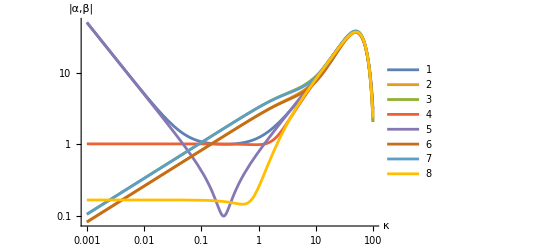

```mathematica
ClearAll[kk,Ω,mbb0,mss0,ξss,ξbb,Ω0,τ0,δ];
Ω2f = 50;
plotvals={Ω0-> Ω2f ,mss0-> 10.0,ξss-> -3,δ-> 0.1};
αvals = αsols/.plotvals/.k-> κ k0/.k0-> 1;
LogLogPlot[Evaluate[ Abs/@{azz,azs,asz,ass, bzz,bzs,bsz,bss}/.plotvals/.αvals/.κ-> kk],{kk,10^-3,10^2},PlotLegends->Automatic,AxesLabel->{"κ","|α,β|"}]
```

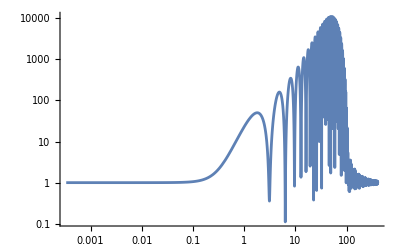

```mathematica
LogLogPlot[Evaluate[Abs[azz+ bzz]^2+Abs[azs+ bzs]^2/.plotvals/.αvals/.κ-> kk],{kk,Exp[-8],Exp[6]}]
```